```mathematica
g[τ_]:=1/(2+1/τ)
PLb[L_,p_]:=1-(1-2p)*Sum[p^i/(i!)*D[p^L/(1-p),{p,i}],{i,1,L-1}]
COV[p_]:=1/(1-2p)^2
PLb2[L_,τ_]:=1-(1-2*g[τ])*Sum[g[τ]^i/(i!)*D[g[τ]^L/(1-g[τ]),{τ,i}],{i,1,L-1}]*COV[g[τ]]^(L-1)
Pl[l_,p_]:=p^l(1-2*p)
PL[L_,p_]:=(1-2*p)*(p^L)/(1-p)
Plb[l_,p_]:=(1-p)*(p^l)/(l!)*D[(p^(l+1))/(1-p),{p,l}]

Plb2[l_,τ_]:=(1-2*g[τ])*g[τ]^l/(l!)*D[(g[τ]^(l+1))/(1-g[τ]),{τ,l}]*COV[g[τ]]
```

```mathematica
Plb[0,p]
```

p

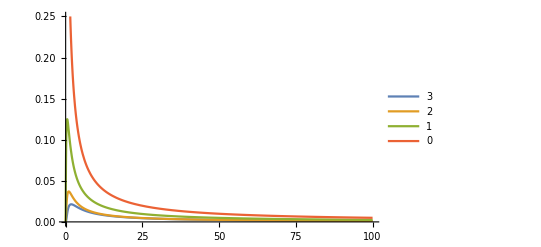

```mathematica
Plot[{PL[3,g[τ]],Pl[2,g[τ]], Pl[1,g[τ]],Pl[0,g[τ]]},{τ,0,100},PlotRange->{0,0.25},PlotLegends->{"3","2","1","0"}]
```

```mathematica
-0.19999999999999996 ∂_{1.2,0} (-6.000000000000001
```

General::ivar: 0.0000204286 is not a valid variable.

D::dvar: Multiple derivative specifier {0.0000204286, 0.} does not have the form {variable, n}, where n is a non-negative machine integer.

General::ivar: 0.0204286 is not a valid variable.

D::dvar: Multiple derivative specifier {0.0204286, 0.} does not have the form {variable, n}, where n is a non-negative machine integer.

General::ivar: 0.0408368 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

D::dvar: Multiple derivative specifier {0.0408368, 0.} does not have the form {variable, n}, where n is a non-negative machine integer.

General::stop: Further output of D :: dvar will be suppressed during this calculation.

-Graphics-